Q: How often should Player 1 bluff?
A: Enough to make Player 2 indifferent to calling or folding.
EV_call = EV_fold

P: initial pot = 1
S: bet size as proportion of pot.
p_(bluff:)probability of bluff

EV_call:1+S (pot + bet) when calling a bluff; -S when calling a value bet
EV_fold: 0

```mathematica
Subscript[EV, call]=Subscript[p, bluff](1+S) - (1-Subscript[p, bluff]) S
```

```mathematica
Setting Subscript[EV, call]= Subscript[EV, fold] :
```

```mathematica
Subscript[p, bluff] (1+S) - (1-Subscript[p, bluff])  S== 0
```

```mathematica
Solve[Subscript[p, bluff] (1+S) - (1-Subscript[p, bluff])  S== 0, Subscript[p, bluff]]
```

Solve[(S (1+S))/(1+2 S)-S (1-S/(1+2 S))==0,S/(1+2 S)]

```mathematica
o_(bluff:)ratio of bluffs to checks, or odds of bluff expressed as x:1
Subscript[o, bluff]= Subscript[p, bluff]/(1-Subscript[p, bluff])
```

```mathematica
Subscript[p, bluff] = S/(1+2S);
```

```mathematica
Subscript[o, bluff] = Subscript[p, bluff]/(1-Subscript[p, bluff])
```

S/((1+2 S) (1-S/(1+2 S)))

```mathematica
Simplify[Subscript[o, bluff]]
S/(1+S)
```

```mathematica
We' ll use this, because it's simpler. 
Given number or probability of value bets, we want S/(1+S)as many bluffs.
```

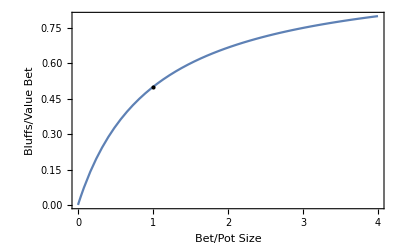

```mathematica
bluffratio[s_] = s/(1+s);
g1 = Plot[{bluffratio[S]}, {S, 0,4}, Frame->True, FrameLabel->{"Bet/Pot Size", "Bluffs/Value Bet"}];
g2 = Graphics[Point[{1, 0.5}]];
Show[g1,g2]
```

```mathematica
Needs["Plotly"]
Plotly[bluffratio[S], {S, 0,4}, Frame->True, FrameLabel->{"Bet/Pot Size", "Bluffs/Value Bet"}]
```

Needs[Plotly]

```mathematica
Q : How often should Player 2 call?
A : Often enough to make Player 1 indifferent to bluffing

Subscript[EV, bluff]=Subscript[EV, call]
Subscript[p, call] : call probability
(1 - Subscript[p, call]) : fold probability
P = 1
S = B/P
```

```mathematica
Subscript[EV, bluff]== (1-Subscript[p, call])P - Subscript[p, call] B
divide by P
Subscript[EV, bluff]== (1-Subscript[p, call]) - Subscript[p, call] S
Subscript[EV, fold]== 0
```

```mathematica
Solve[(1-Subscript[p, call])-Subscript[p, call] S==0,Subscript[p, call]]
```

{{p_call→1/(1+S)}}

1/(1+s)

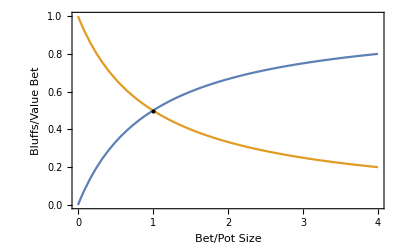

```mathematica
callprob[s_]= 1/(1+s)
g1 = Plot[{bluffratio[S],callprob[S]}, {S, 0, 4}, Frame->True, FrameLabel->{"Bet/Pot Size", "Bluffs/Value Bet"}];
g2 = Graphics[Point[{1, 0.5}]];
Show[g1,g2]
```

```mathematica
Needs["Plotly"]
Plotly[{bluffratio[S],callprob[S]}, {S, 0, 4}]
```

InvisiblePrefixScriptBase[Needs][Plotly]

```mathematica
ev[bluffratio_, callprob_, s_]=0.5(1+callprob s)+0.5bluffratio((1-callprob)-callprob s);
Plot3D[ev[b, c, 0], {b, 0, 1}, {c, 0, 1}, BoxRatios->1 , Axes->True, AxesLabel->{"Bluff Ratio", "Call %", "Expected Value"}, PlotRange->{0,1}]
```

-Graphics3D-

```mathematica
Animate[Plot3D[ev[b, c, s], {b, 0, 1}, {c, 0, 1}, BoxRatios->1 , Axes->True, AxesLabel->{"Bluff Ratio", "Call %", "Expected Value"}, PlotRange->{0,1}], {s, 0, 1}]
```

```mathematica
Export["C:\\Temp\\test.avi", Animate[Plot3D[ev[b, c, s], {b, 0, 1}, {c, 0, 1}, BoxRatios->1 , Axes->True, AxesLabel->{"Bluff Ratio", "Call %", "Expected Value"}, PlotRange->{0,1}], {s, 0, 1}]]
```

C:\Temp\test.avi